```mathematica
(* Statistics generated with no output, 200 frames, one normal force, one gravity force *)
```

```mathematica
GPUtiming={{1,1.853},{2,3.671},{4,9.293},{8,33.655},{16,107.01}};
CPUtiming={{1,3.128},{2,10.128},{4,37.964},{8,149.13},{16,1037.28}};
```

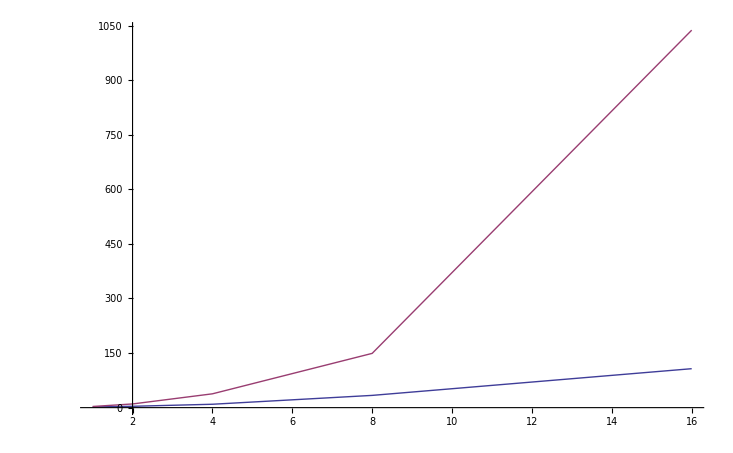

```mathematica
ListLinePlot[{GPUtiming,CPUtiming},PlotRange->All]
```

```mathematica
GPUfit=FindFit[GPUtiming,a(x^b),{a,b},x]
CPUfit=FindFit[CPUtiming,a(x^b),{a,b},x]
```

{a→0.996094,b→1.68697}

{a→0.505664,b→2.75045}

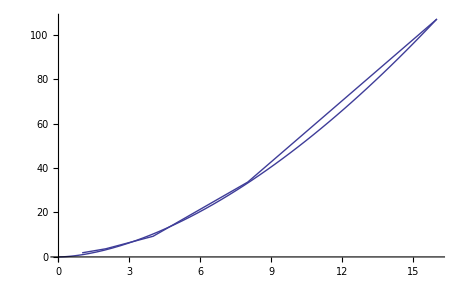

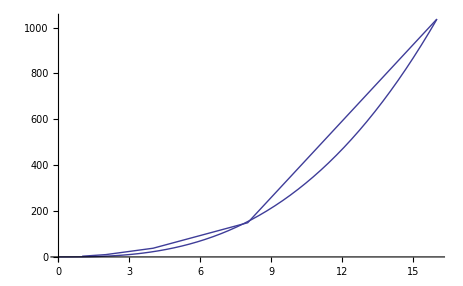

```mathematica
Show[ListLinePlot[GPUtiming],Plot[a(x^b)/.GPUfit,{x,0,16}]]
Show[ListLinePlot[CPUtiming],Plot[a(x^b)/.CPUfit,{x,0,16}]]
```

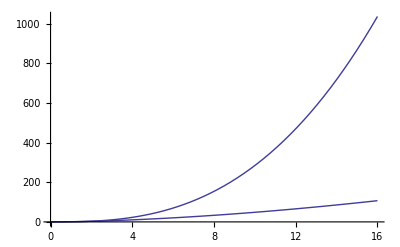

```mathematica
Plot[a(x^b)/.#&/@{GPUfit,CPUfit},{x,0,16}]
```